```mathematica
dir=NotebookDirectory[];
dir=dir<>"data/"
```

/home/nicolas/git/spectrum_quasicrystals/hierarchical chain/data/

## <r^2(t)>, calcul numérique

### États propres dans la base atomique

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
ClearAll[A,v,r];
A[i_,v_,r_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_,v_,r_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->A[i,v,r],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* états propres et leurs énergies dans la base atomique *)
valvec[v_,r_,i_]:=Eigensystem[h[i,v,r]]
```

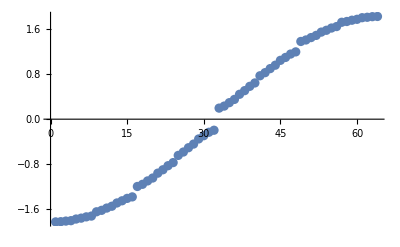

```mathematica
(* le spectre est bien comme on l'attend *)
ListPlot[Sort[valvec[.9,.9,6][[1]]]]
```

```mathematica
(* les vecteurs propres sont bien normalisés à 1 *)
Norm/@valvec[.1,.001,5][[2]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### <r^2> at each site at the same time

```mathematica
(* calcule les probabilités de retour à chaque site *)
rmoy=Block[{n=5,v=.3,r=.3,val,vec,K,tmax=35,dt=.2,timelist,rmoy,d,dtot},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
(* on place l'origine au bord gauche de la chaîne *)
dtot=Sum[A[i,v,r]^-1,{i,2^n}];
d=dtot^-1 ParallelTable[Sum[A[i,v,r]^-1,{i,j}],{j,2^n-1}];
(* ne pas oublier l'origine en 0 ! *)
PrependTo[d,0];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
(* matrice K : propagateur *)
K=ParallelTable[Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[j]]],{k,2^n}],{t,timelist},{i,2^n},{j,2^n}];
(* diffusion : <r^2>_i = Subscript[Σ, j] (Subscript[d, j]-Subscript[d, i])^2 Subscript[(K^*), ji] Subscript[K, ji] *)
rmoy=Table[Sum[Abs[(d[[j]]-d[[i]])K[[timeIt,j,i]]]^2,{j,2^n}],{i,2^n},{timeIt,Length@timelist}]
];
```

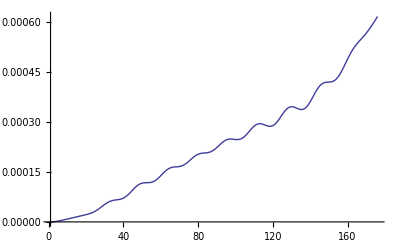

```mathematica
ListPlot[rmoy[[2^4]],Joined->True,PlotRange->All]
```

### <r^2> at one selected site

#### Periodic chain

```mathematica
(* calcule les probabilités de retour au site en milieu de chaîne *)
{rmiddlep,intp}=Block[{n=7,v=1.,r=1.,val,vec,K,tmax=80,dt=.5,timelist,rmiddle,middle,d,dtot,int},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
(* on place l'origine au bord gauche de la chaîne *)
dtot=Sum[A[i,v,r]^-1,{i,2^n}];
d=dtot^-1 ParallelTable[Sum[A[i,v,r]^-1,{i,j}],{j,2^n-1}];
(* ne pas oublier l'origine en 0 ! *)
PrependTo[d,0];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
middle=2^(n-1)+1;
(* matrice K : propagateur *)
K=ParallelTable[Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[middle]]],{k,2^n}],{t,timelist},{i,2^n}];
(* diffusion : <r^2>_i = Subscript[Σ, j] (Subscript[d, j]-Subscript[d, i])^2 Subscript[(K^*), ji] Subscript[K, ji] *)
rmiddle=Table[Sum[Abs[(j-middle)K[[timeIt,j]]]^2,{j,2^n}],{timeIt,Length@timelist}];
(* intensité au bord/intensité au milieu de la chaîne *)
int=Abs[(Transpose[K][[1]])/(Transpose[K][[middle]])];
(* temps et proba de retour, temps et intensité relative *)
{MapThread[{#1,#2}&,{timelist,rmiddle}],MapThread[{#1,#2}&,{timelist,int}]}
];
```

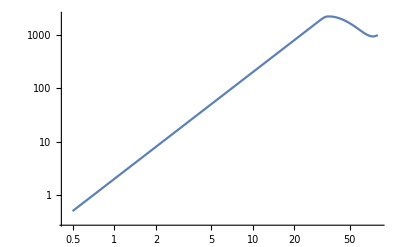

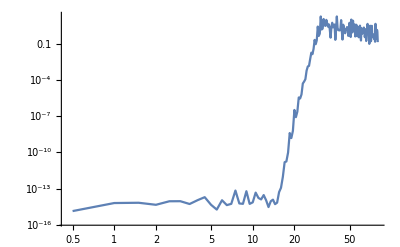

```mathematica
ListLogLogPlot[rmiddlep,Joined->True,PlotRange->All]
ListLogLogPlot[intp,PlotRange->All,Joined->True]
```

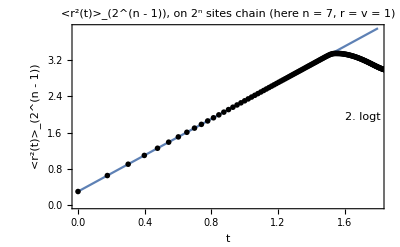

FittedModel[0.30103+2. logt]

```mathematica
(* power law fit *)
ClearAll[dat,fit];dat=rmiddlep;
xi=2;xf=40;
fit=LinearModelFit[Log10@dat[[xi;;xf]],logt,logt];
Plot[Normal@fit,{logt,0,1.8},Axes->False,Frame->True,Epilog->{PointSize@.01,Point@Log10@Drop[dat,1]},PlotLabel->"<r^2(t)>_(2^(n - 1)), on 2^n sites chain (here n = 7, r = v = 1)",AxesLabel->{t,"<r^2(t)>_(2^(n - 1))"},PlotLegends->Placed[Chop[Normal@fit-(Normal@fit/.logt->0)],{Right,Center}]]
Export[dir<>"diffusion_7_periodic_fit.pdf",%];
fit
```

#### Hierarchical chain

```mathematica
(* calcule les probabilités de retour au site en milieu de chaîne *)
{rmiddle,int}=Block[{n=10,v=.3,r=.3,val,vec,K,tmax=1500,dt=5.,timelist,rmiddle,middle,d,dtot,int},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
(* on place l'origine au bord gauche de la chaîne *)
dtot=Sum[A[i,v,r]^-1,{i,2^n}];
d=dtot^-1 ParallelTable[Sum[A[i,v,r]^-1,{i,j}],{j,2^n-1}];
(* ne pas oublier l'origine en 0 ! *)
PrependTo[d,0];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
middle=2^(n-1)+1;
(* matrice K : propagateur *)
K=ParallelTable[Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[middle]]],{k,2^n}],{t,timelist},{i,2^n}];
(* diffusion : <r^2>_i = Subscript[Σ, j] (Subscript[d, j]-Subscript[d, i])^2 Subscript[(K^*), ji] Subscript[K, ji] *)
rmiddle=Table[Sum[Abs[(j-middle)K[[timeIt,j]]]^2,{j,2^n}],{timeIt,Length@timelist}];
(* intensité au bord/intensité au milieu de la chaîne *)
int=Abs[(Transpose[K][[1]])/(Transpose[K][[middle]])];
(* temps et proba de retour, temps et intensité relative *)
{MapThread[{#1,#2}&,{timelist,rmiddle}],MapThread[{#1,#2}&,{timelist,int}]}
];
```

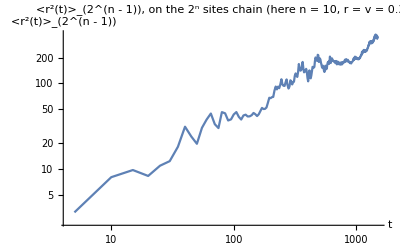

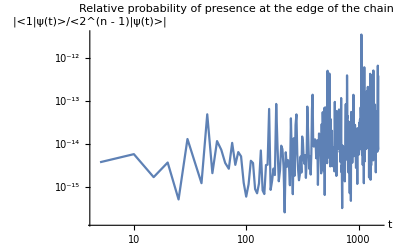

```mathematica
ListLogLogPlot[rmiddle,Joined->True,PlotRange->All,PlotLabel->"<r^2(t)>_(2^(n - 1)), on the 2^n sites chain (here n = 10, r = v = 0.3)",AxesLabel->{t,"<r^2(t)>_(2^(n - 1))"}]
Export[dir<>"diffusion_10.pdf",%];
ListLogLogPlot[int,PlotRange->All,Joined->True,PlotLabel->"Relative probability of presence at the edge of the chain",AxesLabel->{t,"|<1|ψ(t)>/<2^(n - 1)|ψ(t)>|"}]
Export[dir<>"diffusion_10_prob.pdf",%];
```

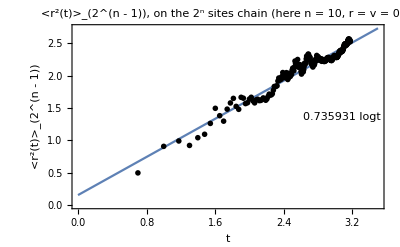

FittedModel[0.155856+0.735931 logt]

```mathematica
(* power law fit *)
ClearAll[dat,fit];dat=rmiddle;
xi=2;xf=Floor[1500/5];
fit=LinearModelFit[Log10@dat[[xi;;xf]],logt,logt];
Plot[Normal@fit,{logt,0,3.5},Axes->False,Frame->True,Epilog->{PointSize@.01,Point@Log10@Drop[dat,1]},PlotLabel->"<r^2(t)>_(2^(n - 1)), on the 2^n sites chain (here n = 10, r = v = 0.3)",AxesLabel->{t,"<r^2(t)>_(2^(n - 1))"},PlotLegends->Placed[Chop[Normal@fit-(Normal@fit/.logt->0)],{Right,Center}]]
Export[dir<>"diffusion_10_fit.pdf",%];
fit
```

### Evolution of intensity and amplitude

```mathematica
(* évolution de l'intensité sur la chaîne !! *)
ClearAll[n,v,r,val,vec,K,tmax,dt,timelist,rmiddle,middle,d,dtot,it,int];
Module[{n=8,v=1.,r=1.,val,vec,K,tmax=80,dt=.5,timelist,middle,d,dtot,int,posint,plots},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
(* on place l'origine au bord gauche de la chaîne *)
dtot=Sum[A[i,v,r]^-1,{i,2^n-1}];
d=dtot^-1 ParallelTable[Sum[A[i,v,r]^-1,{i,j}],{j,2^n-1}];
(* ne pas oublier l'origine en 0 ! *)
PrependTo[d,0];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
middle=2^(n-1);
(* matrice K : propagateur *)
K=ParallelTable[Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[middle]]],{k,2^n}],{t,timelist},{i,2^n}];
(* intensité absolue *)
int=Abs[K]^0.6;
(* table des positions et des intensités *)
posint=Table[MapThread[{#1,#2}&,{d,int[[t]]}],{t,Length@timelist}];
(* position et intensité absolue à un instant donné *)
(*Manipulate[ListPlot[posint[[t]],PlotRange->{0,1}],{t,Length@timelist}]*)
plots=ParallelMap[ListPlot[#,PlotRange->{0,1},Joined->True,PlotStyle->PointSize[.0025]]&,posint];
Export["animate.avi",plots,ImageResolution->300];
]
```

```mathematica
(* évolution de l'amplitude sur la chaîne !! *)
ClearAll[n,v,r,val,vec,K,tmax,dt,timelist,rmiddle,middle,d,dtot,it,int];
posint=Module[{n=7,v=1.,r=1.,val,vec,K,tmax=10,dt=.2,timelist,middle,d,dtot,int,posint,plots,ax,ay},
(* on prend des distances entre sites ppv proportionnelles aux amplitudes de saut *)
(* on place l'origine au bord gauche de la chaîne *)
dtot=Sum[A[i,v,r]^-1,{i,2^n-1}];
d=dtot^-1 ParallelTable[Sum[A[i,v,r]^-1,{i,j}],{j,2^n-1}];
(* ne pas oublier l'origine en 0 ! *)
PrependTo[d,0];
{val,vec}=valvec[v,r,n];
timelist=Range[0,tmax,dt];
middle=2^(n-1);
(* matrice K : propagateur *)
K=ParallelTable[Sum[Exp[-I t val[[k]]]*vec[[k]][[i]]*Conjugate[vec[[k]][[middle]]],{k,2^n}],{t,timelist},{i,2^n}];
(* intensité absolue *)
ax=Re[K];
ay=Im[K];
(* table des positions et des intensités *)
posint=Table[MapThread[{#1,#2}&,{d,ax[[t]]}],{t,Length@timelist}]
(* position et intensité absolue à un instant donné *)
(*Manipulate[ListPlot[posint[[t]],PlotRange->{0,1}],{t,Length@timelist}]*)
];
```

```mathematica
plots=ParallelMap[ListPlot[#,PlotRange->{-.8,.8},Joined->False,PlotStyle->PointSize[.006]]&,posint];
```

```mathematica
Export["ampli.avi",plots,ImageResolution->300];
```